Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1.  Floating point. Write 84.175, -528.685, 0.000924138, and -362005 in floating-point form, rounded to 5S (5 significant digits).

```mathematica
Clear["Global`*"]
```

```mathematica
ScientificForm[{84.175,-528.685,0.000924138,-362005.},5]
```

{8.4175×10^1,-5.2868×10^2,9.2414×10^-4,-3.6201×10^5}

I almost gave the cell the greenie because the significant digits are shown correctly. But as for the text’s odd penchant for showing a zero to the left of the decimal point, I don’t know how to imitate that.

3.  Small differences of large numbers may be particularly strongly affected by rounding errors. Illustrate this by computing 0.81534/(35*724 -35.596) as given with 5S, then rounding stepwise to 4S, 3S, and 2S, where “stepwise” means round the rounded numbers, not the given ones.

```mathematica
Clear["Global`*"]
```

It took a little while to figure out what was wanted. An extra difficulty is a typo in the problem, which can be seen in the first cell below.

```mathematica
ScientificForm[0.81534/(35.724-35.596),5]
```

6.3698

```mathematica
ScientificForm[0.8153/(35.72-35.6),4]
```

6.794

```mathematica
ScientificForm[0.815/(35.7-35.6),3]
```

8.15

```mathematica
ScientificForm[0.82/(36-36),2]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

The green cells above match the answers in the text.

5.  Rounding and adding. Let a_1,. . . ,a_n be numbers with a_j correctly rounded to S_j digits. In calculating the sum a_1+ . . . +a_n, retaining S = min S_j significant digits, is it essential that we first add and then round the result, or that we first round each number to S significant digits and then add?

Add first.

7.  Quadratic equation. Solve x^2 - 30 x+1 by (4) and by (5), using 6S in the computation. Compare and comment.

```mathematica
pol[x_]=x^2-30 x+1
```

1-30 x+x^2

```mathematica
N[Solve[pol[x]==0,x],6]
```

{{x→0.0333705},{x→29.9666}}

Numbered line (5) has the content that x_1 = c/(a x_2), where x_1 is the first sol’n above, and x_2 is the second. As the below cell shows, in the present case the sol’ns for x_1 turn out to be apparently the same (for a=c=1). If significant digits had not been imposed, the sol’ns would have been exactly the same, since all was rational. Even if truncated to output precision, the sol’n (of x1e) shows no alteration.

```mathematica
x1=1/(1 29.96662954709576554233499492926619720702`6.)
```

0.0333705

```mathematica
x1e=1/(1 29.9666)
```

0.0333705

9.  Do the computations in problem 7 with 4S and 2S.

```mathematica
N[Solve[pol[x]==0,x],4]
```

{{x→0.03337},{x→29.97}}

```mathematica
N[Solve[pol[x]==0,x],2]
```

{{x→0.033},{x→30.}}

The above cells show a slight effect of rounding.

11. Theorems on errors. Prove theorem 1(a) for addition.

Hey, I guessed this one right. And added a couple of examples to test out the idea versus subtraction.

```mathematica
Abs[ϵ]=Abs[x+y-(x̃+ỹ)]=Abs[x-x̃+y-ỹ]=Abs[Subscript[ϵ, x]+Subscript[ϵ, y]]≤Abs[Subscript[ϵ, x]]+Abs[Subscript[ϵ, y]]≤Subscript[β, x]+Subscript[β, y]
```

```mathematica
e=Abs[1+2-(0.99+2.01)]
```

0.

```mathematica
e=Abs[1-2-(0.99-2.01)]
```

0.02

13.  Division. Prove theorem 1(b) for division.

I can’t follow this proof, even though it is complete in the text answer.

15.  Logarithm. Compute Log[a] - Log[b] with 6S arithmetic for a = 4.00000 and b = 3.99900 (a) as given and (b) from Log[a/b].

```mathematica
Clear["Global`*"]
```

First I do the separate calculations

```mathematica
N[Log[4.00000],6]
```

1.38629

```mathematica
N[Log[3.99900],6]
```

1.38604

and make a subtraction. Though Mathematica shows lots of decimal places, the calculation itself was only performed to six significant digits. But the difference of these two intermediate results equals the precision of the Log of the divided starting values. Probably because default machine precision gives better precision than demanded.

```mathematica
1.3862943611198906-1.3860443298646814
```

0.000250031

If I only subtract the two results, both to the requested accuracy of six places, then there is a difference compared to the Log of the divided starting values, but not in the decimals of requested significance.

```mathematica
NumberForm[1.38629-1.38604,{6,9}]
```

0.000250000

```mathematica
N[Log[4.00000/3.99900],6]
```

0.000250031

19.  Exponential function. Calculate 1/ⅇ = 0.367879 6(S) from the partial sums of 5 - 10 terms of the Maclaurin series (a) of ⅇ^-x with x = 1, (b) of ⅇ^x with x = 1 and then taking the reciprocal. Which is more accurate?

```mathematica
Clear["Global`*"]
```

```mathematica
mackee=Normal[Series[ⅇ^-x,{x,0,5}]]
```

1-x+x^2/2-x^3/6+x^4/24-x^5/120

```mathematica
N[mackee]/.x->1
```

0.366667

```mathematica
mackeep=Normal[Series[ⅇ^x,{x,0,5}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

```mathematica
1/(N[mackeep]/.x->1)
```

0.368098

Yes, the difference looks significant. I would have missed the guess about which is more accurate. The below cells confirm the text claim that the reciprocal is more accurate in this instance.

```mathematica
mackeeL=Normal[Series[ⅇ^-x,{x,0,50}]];
```

```mathematica
N[mackeeL]/.x->1
```

0.367879

```mathematica
0.3678794411714424-0.3666666666666667
```

0.00121277

```mathematica
0.3678794411714424-0.36809815950920244
```

-0.000218718

21. Binary conversion. Show that 23 = 20*10^1 + 3*10^0 = 16 + 4 + 2 +1 = 2^4 + 2^2 + 2^1 + 2^0 = (1 0 1 1 (1.))_2 can be obtained by the division algorithm 
2⌊23 | remainder 1=c_0
2⌊11 | remainder 1=c_1
2⌊5 | remainder 1=c_2
2⌊2 | remainder 0=c_3
0 | remainder 1=c_4

```mathematica
BaseForm[23,2]
```

10111_2

The above answer, with unauthorized total dependence on Mathematica, agrees with the text answer.

23.  Show that 0.1 is not a binary machine number.

```mathematica
Clear["Global`*"]
```

```mathematica
BaseForm[0.1,2]
```

0.00011001100110011001101_2

Not exactly the same argument as the text answer.

25.  CAS experiment. Approximations. Obtain x=0.1=3/2∑_(m=1)^∞ 2^(-4m) from problem 23. Which machine number (partial sum) S_n will first have the value 0.1 to 30 decimal digits?

Okay, what am I doing here? Starting from the right. The table is taking n from 1 to 15, and n also governs the number of terms in the Sum, the more terms, the more precision. The {60, 30} under NumberForm specifies 60 digits of precision and 30 digits shown to the right of the decimal point. The answer to the problem question is that S_n=13, with 13 terms, 13 partial sums to a precision of 30 decimal digits. The block of numbers would look more impressive if I knew how to progressively suppress the vacant zeros on the right, but I didn’t find an easy way.

```mathematica
Clear["Global`*"]
```

```mathematica
TableForm[Table[{n,NumberForm[N[3/2 Sum[2^(-4 m),{m,1,n}]],{60,30}]},{n,1,15}]]
```

1 | 0.093750000000000000000000000000
2 | 0.099609375000000000000000000000
3 | 0.099975585937500000000000000000
4 | 0.099998474121093800000000000000
5 | 0.099999904632568400000000000000
6 | 0.099999994039535500000000000000
7 | 0.099999999627471000000000000000
8 | 0.099999999976716900000000000000
9 | 0.099999999998544800000000000000
10 | 0.099999999999909100000000000000
11 | 0.099999999999994300000000000000
12 | 0.099999999999999600000000000000
13 | 0.100000000000000000000000000000
14 | 0.100000000000000000000000000000
15 | 0.100000000000000000000000000000

I don’t understand why the text says it will take 26 terms to get to the desired accuracy. It looks to me like it takes exactly half that many.

27.  Backward recursion. In problem 26. Using ⅇ^x < ⅇ (0 < x < 1), conclude that Abs[I_n]≤ⅇ/(n+1)→0 as n→∞. Solve the iteration formula for  I_(n-1)=(ⅇ-I_n)/n, start from I_15≈0 and compute 4S values of I_14,I_13,. . .,I_1 .

```mathematica
Clear["Global`*"]
```

As for the function in question, the integral value looks murky.

```mathematica
eyen=Integrate[ⅇ^x x^n,{x,0,1}]
```

ConditionalExpression[(-1)^(1-n) (Gamma[1+n]-ⅇ Subfactorial[n]),Re[n]>-1]

However, it is not hard for me to accept that the inequality, as seen in a plot, is true regarding eyen and ⅇ/(n+1). That is, eyen is clearly less than ⅇ/(n+1), which tends to zero.

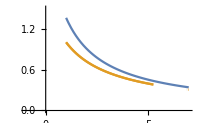

```mathematica
Plot[{ⅇ/(n+1),Table[{eyen},{x,0,1}]},{n,1,7},ImageSize->200,PlotRange->{{-1,7},{0,1.5}}]
```

```mathematica
Limit[ⅇ/(n+1),n->∞]
```

0

I need to get the recursive terms.  I’d like to get Mathematica to spit out a neat table following a do-loop, but for now I have to settle for doing the numbers by hand.

```mathematica
I13=N[(ⅇ-0.1812)/14]
```

0.18122

```mathematica
I12=N[(ⅇ-0.1812)/13]
```

0.19516

The final digit in the above number makes it yellow.

```mathematica
I11=N[(ⅇ-0.1952)/12]
```

0.210257

```mathematica
I10=N[(ⅇ-0.2103)/11]
```

0.227998

```mathematica
I9=N[(ⅇ-0.2280)/10]
```

0.249028

```mathematica
I8=N[(ⅇ-0.2490)/9]
```

0.274365

```mathematica
I7=N[(ⅇ-0.2744)/8]
```

0.305485

```mathematica
I6=N[(ⅇ-0.3055)/7]
```

0.344683

```mathematica
I5=N[(ⅇ-0.3447)/6]
```

0.395597

```mathematica
I4=N[(ⅇ-0.3956)/5]
```

0.464536

```mathematica
I3=N[(ⅇ-0.4645)/4]
```

0.563445

```mathematica
I2=N[(ⅇ-0.5634)/3]
```

0.718294

```mathematica
I1=N[(ⅇ-0.7183)/2]
```

0.999991

I could not get I15 so I’ll compensate by throwing in I0. At least it will make the grid match up.

```mathematica
I0=N[(ⅇ-1.000)/1]
```

1.71828

The table. The table in g2 below provides the first four columns in the grid.  The last column has S4 numbers, the basic idea behind the problem. So if the 4th column is compared with the last column, an accumulating margin of error is observed.

```mathematica
eyeb=Sort[{0.181220,0.19516,0.210257,0.227998,0.249028,0.274365,0.305485,0.344683,0.395597,0.464536,0.563445,0.718294,0.999991,1.71828,"null"},Greater]
```

{1.71828,0.999991,0.718294,0.563445,0.464536,0.395597,0.344683,0.305485,0.274365,0.249028,0.227998,0.210257,0.19516,0.18122,null}

```mathematica
eyeb4=Sort[{0.1812,0.1952,0.2103,0.2280,0.2490,0.2744,0.3055,0.3447,0.3956,0.4645,0.5634,0.7183,1.000,1.718,"null"},Greater]
```

{1.718,1.,0.7183,0.5634,0.4645,0.3956,0.3447,0.3055,0.2744,0.249,0.228,0.2103,0.1952,0.1812,null}

```mathematica
g1=Grid[{{Nr , Equa ,"Sm.",".Table.","..Hand .",Hand S^4}},Frame->All];
```

```mathematica
g2=Grid[Table[{n,HoldForm[(ⅇ-ⅇ/(n+1))/n],(ⅇ-ⅇ/(n+1))/n,N[(ⅇ-ⅇ/(n+1))/n],eyeb[[n]],eyeb4[[n]]},{n,15,1,-1}],Frame->All];
```

```mathematica
Grid[{{g1},{g2}}]
```

Nr | Equa | Sm. | .Table. | ..Hand . | Hand S^4
15 | (ⅇ-ⅇ/(n+1))/n | ⅇ/16 | 0.169893 | null | null
14 | (ⅇ-ⅇ/(n+1))/n | ⅇ/15 | 0.181219 | 0.18122 | 0.1812
13 | (ⅇ-ⅇ/(n+1))/n | ⅇ/14 | 0.194163 | 0.19516 | 0.1952
12 | (ⅇ-ⅇ/(n+1))/n | ⅇ/13 | 0.209099 | 0.210257 | 0.2103
11 | (ⅇ-ⅇ/(n+1))/n | ⅇ/12 | 0.226523 | 0.227998 | 0.228
10 | (ⅇ-ⅇ/(n+1))/n | ⅇ/11 | 0.247117 | 0.249028 | 0.249
9 | (ⅇ-ⅇ/(n+1))/n | ⅇ/10 | 0.271828 | 0.274365 | 0.2744
8 | (ⅇ-ⅇ/(n+1))/n | ⅇ/9 | 0.302031 | 0.305485 | 0.3055
7 | (ⅇ-ⅇ/(n+1))/n | ⅇ/8 | 0.339785 | 0.344683 | 0.3447
6 | (ⅇ-ⅇ/(n+1))/n | ⅇ/7 | 0.388326 | 0.395597 | 0.3956
5 | (ⅇ-ⅇ/(n+1))/n | ⅇ/6 | 0.453047 | 0.464536 | 0.4645
4 | (ⅇ-ⅇ/(n+1))/n | ⅇ/5 | 0.543656 | 0.563445 | 0.5634
3 | (ⅇ-ⅇ/(n+1))/n | ⅇ/4 | 0.67957 | 0.718294 | 0.7183
2 | (ⅇ-ⅇ/(n+1))/n | ⅇ/3 | 0.906094 | 0.999991 | 1.
1 | (ⅇ-ⅇ/(n+1))/n | ⅇ/2 | 1.35914 | 1.71828 | 1.718

29.  Approximations of π = 3.14159265358979. . . are 22/7 and 355/113. Determine the corresponding errors and relative errors to 3 significant digits.

```mathematica
Clear["Global`*"]
```

```mathematica
tt=NumberForm[N[22/7],{60,30}]
```

3.142857142857143000000000000000

```mathematica
tf=NumberForm[N[355/113],{60,30}]
```

3.141592920353983000000000000000

```mathematica
errort=N[π-"3.142857142857143000000000000000",6]
```

-0.00126449

To three significant digits, this would be

```mathematica
-0.00126
```

And then there is the relative error. The following answer does not agree exactly with the text answer.

```mathematica
relerrort=-0.00126/π
```

-0.00040107

For the other fractional approximation, the error would be

```mathematica
diff=N[π-"3.141592920353983000000000000000",6]
```

-2.66764×10^-7

To three significant digits,  this would be

```mathematica
-2.66*^-7
```

And the relative error would be

```mathematica
relerrorf=(-2.66*^-7)/π
```

-8.46704×10^-8